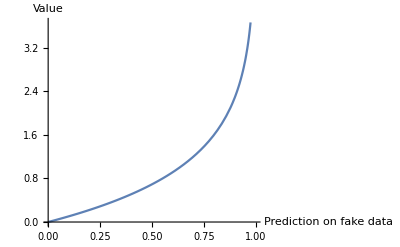

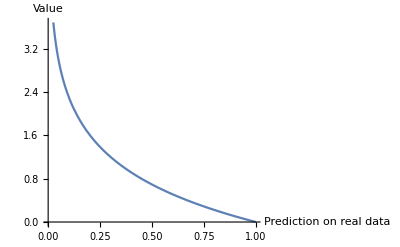

```mathematica
L[p_,y_]:=-(y*Log[p]+(1-y)*Log[1-p])
Plot[L[p,0],{p,0,1}, AxesLabel->{"Prediction on fake data", "Value"}]
Plot[L[p,1],{p,0,1}, AxesLabel->{"Prediction on real data", "Value"}]
```

```mathematica
Plot[{L[p,1],L[p,0]},{p,0,1}, AxesLabel->{"Prediction", "Value"},PlotLabels->Callout[{"Real data","Fake data"} ,Below]]
```

-Graphics-

```mathematica
0.5(L[0.2,0]+L[0.8,1])
```

0.223144